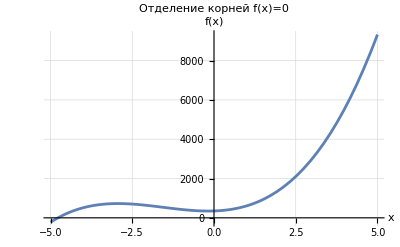

Корень: -4.7733

Число итераций: 8

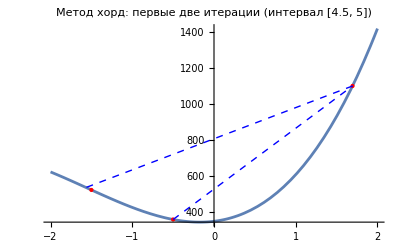

```mathematica
f[x_] :=36x^3+168x^2+55x+350;
p1 = Plot[f[x], {x , -5, 5}, PlotRange -> All, AxesLabel->{"x","f(x)"}, PlotStyle->"Thick", GridLines->"Automatic", PlotLabel->"Отделение корней f(x)=0"];
Show[p1]
Clear[a, b, x0, x1, iter, eps]
a = -1.5; b = -0.5;
x0 = a; x1=b;
eps = 10^-3;
iter=0;
points= {{x0, f[x0]}, {x1, f[x1]}};

While[Abs[x1-x0]>eps,
iter++;
xnew=x1-f[x1](x1-x0)/(f[x1]-f[x0]);
x0=x1; x1=xnew;
AppendTo[points, {x1, f[x1]}]]
Print["Корень: ", N[x1, 10]]
Print["Число итераций: ", iter]


p2 = Plot[f[x], {x, -2, 2}, PlotStyle->"Thick", PlotRange->All, Epilog->{
Red, PointSize[Large],
Point[points[[1 ;; 3]]],
Blue, Dashed,
Line[{points[[3 ;; 4]], points[[2 ;; 3]]}]},
PlotLabel->"Метод хорд: первые две итерации (интервал [4.5, 5])"];
Show[p2]
```